# ConvexityCriteria

## Convexity, radial convexity, and first-hit detection under polygon averaging

## Purpose

This notebook isolates the geometric criteria used in Chapter 2. It tests ordinary convexity using signed areas of consecutive edge vectors, tests strict radial convexity after centering at the centroid, and detects the first iterate of the averaging dynamics satisfying each criterion.

All executable cells are ordinary Wolfram Language Input cells. Typeset box expressions appear only in explanatory cells.

## 1. Polygon and averaging definitions

```mathematica
ClearAll["Global`*"];

applyA[p_List, alpha_?NumericQ] :=
  (1 - alpha) N[p] + alpha RotateLeft[N[p]];

centerPolygon[p_List] :=
  N[p] - Mean[N[p]];

regularPolygon[n_Integer?Positive] :=
  N@Table[Exp[2 Pi I j/n], {j, 0, n - 1}];

polygonPoints[p_List] :=
  N@Transpose[{Re[N[p]], Im[N[p]]}];

polygonPlot[p_List, title_: None] := Module[{pts},
  pts = polygonPoints[p];
  Graphics[
    {
      Thick,
      Line[Append[pts, First[pts]]],
      PointSize[0.018],
      Point[pts]
    },
    Axes -> True,
    AspectRatio -> 1,
    PlotRange -> All,
    PlotLabel -> title,
    ImageSize -> Large
  ]
];
```

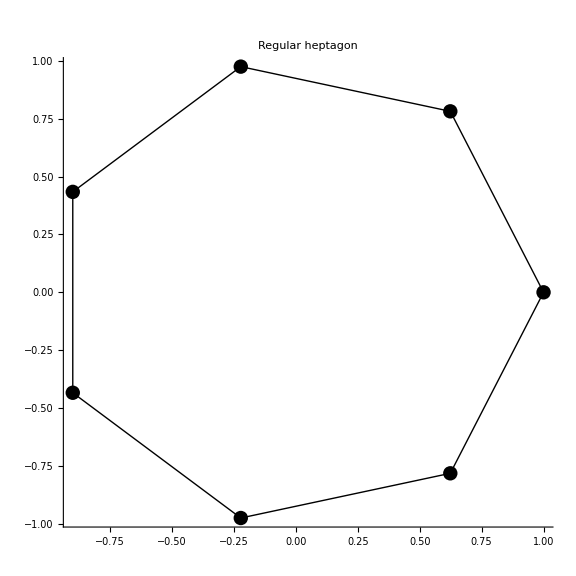

```mathematica
polygonPlot[regularPolygon[7], "Regular heptagon"]
```

## 2. Edge vectors and signed turn areas

For consecutive edges e_j and e_(j+1), the signed planar determinant is

Δ_j=Im(OverBar[e_j]e_(j+1))

```mathematica
edges[p_List] :=
  RotateLeft[N[p]] - N[p];

signedTurnAreas[p_List] := Module[{e, n},
  e = edges[p];
  n = Length[e];
  Chop@N@Table[
    Im[Conjugate[e[[j]]] e[[Mod[j, n] + 1]]],
    {j, 1, n}
  ]
];
```

```mathematica
q = regularPolygon[9];
signedTurnAreas[q]
```

{0.300767,0.300767,0.300767,0.300767,0.300767,0.300767,0.300767,0.300767,0.300767}

## 3. Orientation-sensitive convexity tests

```mathematica
strictlyConvexCCWQ[p_List, tol_: 10^-10] := Module[{a},
  a = signedTurnAreas[p];
  TrueQ[Min[a] > tol]
];

strictlyConvexCWQ[p_List, tol_: 10^-10] := Module[{a},
  a = signedTurnAreas[p];
  TrueQ[Max[a] < -tol]
];

strictlyConvexQ[p_List, tol_: 10^-10] :=
  TrueQ[strictlyConvexCCWQ[p, tol] || strictlyConvexCWQ[p, tol]];

weaklyConvexQ[p_List, tol_: 10^-10] := Module[{a},
  a = signedTurnAreas[p];
  TrueQ[Min[a] >= -tol || Max[a] <= tol]
];

orientation[p_List, tol_: 10^-10] := Which[
  strictlyConvexCCWQ[p, tol], "Counterclockwise",
  strictlyConvexCWQ[p, tol], "Clockwise",
  True, "Mixed or degenerate"
];
```

```mathematica
{
  strictlyConvexCCWQ[q],
  strictlyConvexCWQ[q],
  strictlyConvexQ[q],
  orientation[q]
}
```

{True,False,True,Counterclockwise}

```mathematica
qReverse = Reverse[q];
{
  strictlyConvexCCWQ[qReverse],
  strictlyConvexCWQ[qReverse],
  strictlyConvexQ[qReverse],
  orientation[qReverse]
}
```

{False,True,True,Clockwise}

## 4. Examples of convex, concave, and degenerate polygons

```mathematica
convexExample = regularPolygon[8];
concaveExample = {0, 2, 1 + 0.4 I, 2 I, 0.2 + 1.2 I};
degenerateExample = {0, 1, 2, 2 + I, I};
```

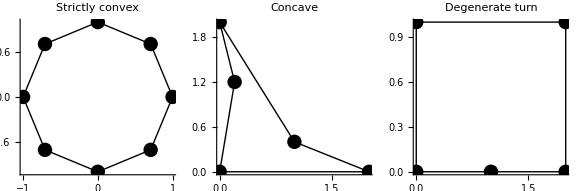

```mathematica
GraphicsRow[
  {
    polygonPlot[convexExample, "Strictly convex"],
    polygonPlot[concaveExample, "Concave"],
    polygonPlot[degenerateExample, "Degenerate turn"]
  },
  ImageSize -> Large
]
```

```mathematica
Dataset@{
  <|"Polygon" -> "Convex", "Signed areas" -> signedTurnAreas[convexExample], "Strictly convex" -> strictlyConvexQ[convexExample]|>,
  <|"Polygon" -> "Concave", "Signed areas" -> signedTurnAreas[concaveExample], "Strictly convex" -> strictlyConvexQ[concaveExample]|>,
  <|"Polygon" -> "Degenerate", "Signed areas" -> signedTurnAreas[degenerateExample], "Strictly convex" -> strictlyConvexQ[degenerateExample]|>
}
```

## 5. Effect of one averaging step

```mathematica
alphaExample = 0.35;
qUpdated = applyA[q, alphaExample];
```

```mathematica
{
  strictlyConvexQ[q],
  strictlyConvexQ[qUpdated],
  signedTurnAreas[qUpdated]
}
```

{True,True,{0.268751,0.268751,0.268751,0.268751,0.268751,0.268751,0.268751,0.268751,0.268751}}

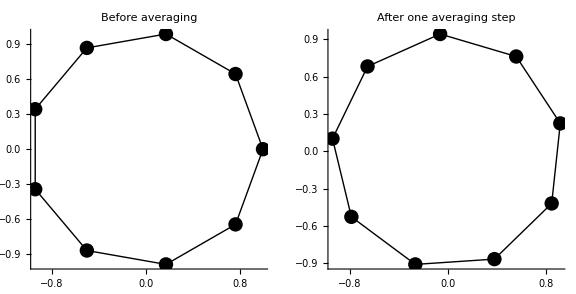

```mathematica
GraphicsRow[
  {
    polygonPlot[q, "Before averaging"],
    polygonPlot[qUpdated, "After one averaging step"]
  },
  ImageSize -> Large
]
```

## 6. First strictly convex iterate

```mathematica
Clear[firstStrictConvexTime];

firstStrictConvexTime[p_List, alpha_?NumericQ] :=
  firstStrictConvexTime[p, alpha, 500];

firstStrictConvexTime[p_List, alpha_?NumericQ, maxM_] /; NumericQ[maxM] := Module[
  {iterate, limit, m},
  iterate = N[p];
  limit = Max[0, Round[maxM]];
  For[m = 0, m <= limit, m++,
    If[TrueQ[strictlyConvexQ[iterate]], Return[m]];
    iterate = applyA[iterate, alpha];
  ];
  Missing["NotFound", limit]
];
```

```mathematica
Length[DownValues[firstStrictConvexTime]]
```

2

```mathematica
SeedRandom[2026];
pExample = RandomReal[{-1, 1}, 12] + I RandomReal[{-1, 1}, 12];
pExample = centerPolygon[pExample];
convexificationTime = firstStrictConvexTime[pExample, alphaExample, 500];
```

```mathematica
convexificationTime
```

10

```mathematica
IntegerQ[convexificationTime]
```

True

```mathematica
convexifiedPolygon = If[
  IntegerQ[convexificationTime],
  Nest[applyA[#, alphaExample] &, pExample, convexificationTime],
  Missing["NoConvexIterate"]
];
```

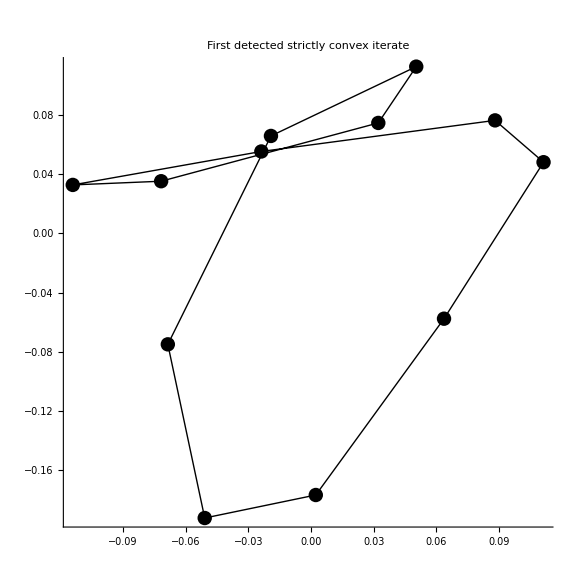

```mathematica
If[
  VectorQ[convexifiedPolygon, NumericQ],
  polygonPlot[convexifiedPolygon, "First detected strictly convex iterate"],
  convexifiedPolygon
]
```

```mathematica
If[
  VectorQ[convexifiedPolygon, NumericQ],
  <|
    "CCW" -> strictlyConvexCCWQ[convexifiedPolygon],
    "CW" -> strictlyConvexCWQ[convexifiedPolygon],
    "Signed areas" -> signedTurnAreas[convexifiedPolygon]
  |>,
  convexifiedPolygon
]
```

<|CCW→False,CW→True,Signed areas→{-0.00750664,-0.00180142,-0.00325058,-0.00141027,-0.000732634,-0.00063512,-0.00366128,-0.00381216,-0.000816194,-0.00539823,-0.00653531,-0.0083055}|>

## 7. Radial angles about the centroid

After centering the polygon at its centroid, strict radial convexity requires nonzero vertices and strictly positive cyclic angle increments.

```mathematica
centeredArguments[p_List] :=
  Arg[centerPolygon[p]];

unwrapAngles[angles_List] := Module[{result, j, candidate},
  result = {First[angles]};
  For[j = 2, j <= Length[angles], j++,
    candidate = angles[[j]];
    While[candidate <= Last[result], candidate += 2 Pi];
    AppendTo[result, candidate];
  ];
  result
];

radialAngleGaps[p_List] := Module[{theta},
  theta = unwrapAngles[centeredArguments[p]];
  Chop@N@Differences[Append[theta, First[theta] + 2 Pi]]
];
```

```mathematica
radialAngleGaps[regularPolygon[10]]
```

{0.628319,0.628319,0.628319,0.628319,0.628319,0.628319,0.628319,0.628319,0.628319,0.628319}

## 8. Strict radial convexity

```mathematica
strictlyRadiallyConvexQ[p_List, tol_: 10^-10] := Module[
  {centered, gaps},
  centered = centerPolygon[p];
  If[!TrueQ[Min[Abs[centered]] > tol], Return[False]];
  gaps = radialAngleGaps[centered];
  TrueQ[Min[gaps] > tol]
];
```

```mathematica
{
  strictlyRadiallyConvexQ[regularPolygon[10]],
  strictlyRadiallyConvexQ[concaveExample],
  radialAngleGaps[concaveExample]
}
```

{True,False,{1.81054,6.04344,2.76109,0.2783,-4.61018}}

## 9. First strictly radially convex iterate

```mathematica
Clear[firstStrictRadialTime];

firstStrictRadialTime[p_List, alpha_?NumericQ] :=
  firstStrictRadialTime[p, alpha, 500];

firstStrictRadialTime[p_List, alpha_?NumericQ, maxM_] /; NumericQ[maxM] := Module[
  {iterate, limit, m},
  iterate = N[p];
  limit = Max[0, Round[maxM]];
  For[m = 0, m <= limit, m++,
    If[TrueQ[strictlyRadiallyConvexQ[iterate]], Return[m]];
    iterate = applyA[iterate, alpha];
  ];
  Missing["NotFound", limit]
];
```

```mathematica
Length[DownValues[firstStrictRadialTime]]
```

2

```mathematica
radialConvexificationTime = firstStrictRadialTime[pExample, alphaExample, 500];
```

```mathematica
radialConvexificationTime
```

Missing[NotFound,500]

```mathematica
IntegerQ[radialConvexificationTime]
```

False

```mathematica
radiallyConvexPolygon = If[
  IntegerQ[radialConvexificationTime],
  Nest[applyA[#, alphaExample] &, pExample, radialConvexificationTime],
  Missing["NoRadiallyConvexIterate"]
];
```

```mathematica
If[
  VectorQ[radiallyConvexPolygon, NumericQ],
  polygonPlot[radiallyConvexPolygon, "First detected strictly radially convex iterate"],
  radiallyConvexPolygon
]
```

Missing[NoRadiallyConvexIterate]

```mathematica
If[
  VectorQ[radiallyConvexPolygon, NumericQ],
  <|
    "Strictly radial" -> strictlyRadiallyConvexQ[radiallyConvexPolygon],
    "Angle gaps" -> radialAngleGaps[radiallyConvexPolygon]
  |>,
  radiallyConvexPolygon
]
```

Missing[NoRadiallyConvexIterate]

## 10. Static evolution gallery

```mathematica
evolutionTimes = {0, 1, 2, 5, 10, 20, 40};
evolutionPolygons = Table[
  Nest[applyA[#, alphaExample] &, pExample, m],
  {m, evolutionTimes}
];
```

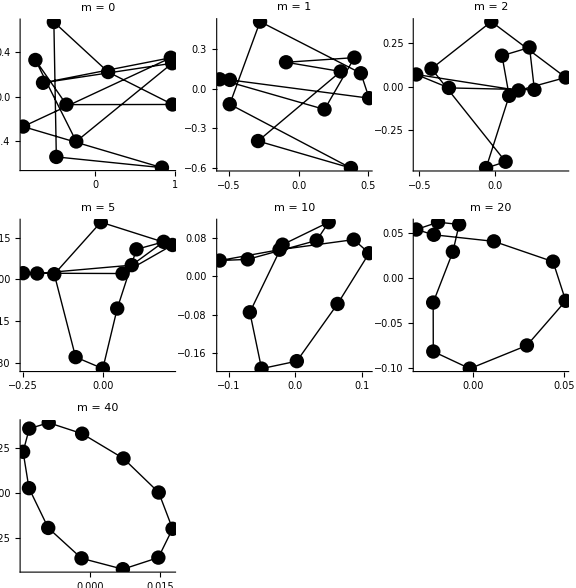

```mathematica
GraphicsGrid[
  Partition[
    MapThread[
      polygonPlot[#1, Row[{"m = ", #2}]] &,
      {evolutionPolygons, evolutionTimes}
    ],
    3,
    3,
    {1, 1},
    Nothing
  ],
  ImageSize -> Large
]
```

## 11. Precomputed animation

```mathematica
animationFrames = Table[
  polygonPlot[
    Nest[applyA[#, alphaExample] &, pExample, m],
    Row[{"Averaging iterate m = ", m}]
  ],
  {m, 0, 60}
];
```

```mathematica
Head[First[animationFrames]]
```

Graphics

```mathematica
ListAnimate[animationFrames, DefaultDuration -> 10]
```

## 12. Automated verification report

```mathematica
Clear[verificationReport];

verificationReport[] := verificationReport[20];

verificationReport[maxN_Integer?Positive] := Module[{rows},
  rows = Table[
    Module[{q, qReverse, alpha, updated, areas, gaps},
      q = regularPolygon[n];
      qReverse = Reverse[q];
      alpha = 0.37;
      updated = applyA[q, alpha];
      areas = signedTurnAreas[q];
      gaps = radialAngleGaps[q];
      <|
        "n" -> n,
        "Regular polygon CCW" -> TrueQ[strictlyConvexCCWQ[q]],
        "Reversal CW" -> TrueQ[strictlyConvexCWQ[qReverse]],
        "Positive signed areas" -> TrueQ[Min[areas] > 0],
        "Averaged polygon convex" -> TrueQ[strictlyConvexQ[updated]],
        "Regular polygon radial" -> TrueQ[strictlyRadiallyConvexQ[q]],
        "Positive radial gaps" -> TrueQ[Min[gaps] > 0]
      |>
    ],
    {n, 3, maxN}
  ];
  Dataset[rows]
];
```

```mathematica
Length[DownValues[verificationReport]]
```

2

```mathematica
verificationReport[]
```

## Conclusion

The notebook provides numerical criteria for strict convexity and strict radial convexity, together with first-hit searches under the averaging dynamics. Signed edge areas detect consistent turning orientation, while centered angular gaps detect radial ordering around the centroid.